# Tarea 6: DFT

Estudiante: José Alfredo de León

Definición de la función de onda Gaussiana normalizada:

```mathematica
ψ[r_]:=2((2 α)/π)^(3/4)Exp[-α r^2]
```

## Cálculo de los distintos términos de funcionales de energía

En esta sección hacemos el álgebra para calculas las diferentes expresiones para cada uno de los términos del funcional de energía electrónica total.

#### Energía cinética por electrón

```mathematica
-π Integrate[ψ[r] 1/2 Laplacian[ψ[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,∞}]
```

ConditionalExpression[(3 α)/2, Re[α]>0]

#### Energía potencial de Coulomb de cada electrón con el núcleo

```mathematica
N[π Integrate[-2/r ψ[r]^2 r^2,{r,0,∞}]]
```

ConditionalExpression[-3.19154 √α, Re[α]>0.]

#### Energía de repulsión entre electrones

Chequeando normalización de la función de onda siguiendo el programa de Thijssen:

```mathematica
Integrate[r^2(√π ψ[r])^2,{r,0,∞}]
```

ConditionalExpression[1, Re[α]>0]

Integramos la ecuación U''(r)=- (u^2(r))/r=-π r ψ^2(r)

```mathematica
Integrate[-π r ψ[r]^2,r]
```

2 ⅇ^(-2 r^2 α) √(2/π) √α

Integramos por segunda vez:

```mathematica
Integrate[2 ⅇ^(-2 r^2 α) √(2/π) √α+c,r]
```

c r+Erf[√2 r √α]

Escribimos la solución de U(r) acorde con las condiciones de frontera U(0)=0 y U(∞)=1.

```mathematica
U=Erf[√2 r √α]
```

Erf[√2 r √α]

Escribimos el potencial de Hartree:

```mathematica
VH=Erf[√2 r √α]/r
```

Erf[√2 r √α]/r

Ahora calculamos ψ V_H ψ

```mathematica
(4π)/4 Integrate[ ψ[r] VH ψ[r] r^2,{r,0,∞}]
```

ConditionalExpression[(2 √α)/(√π), Re[α]>0]

#### Energía de intercambio

Escribimos la densidad electrónica:

```mathematica
n[r_]:=1/2 ψ[r]^2;n[r]
```

(4 √2 ⅇ^(-2 r^2 α) α^(3/2))/π^(3/2)

Calculamos (n(r))^(4/3):

```mathematica
n[r]^(4/3)
```

(8 2^(1/3) (ⅇ^(-2 r^2 α) α^(3/2))^(4/3))/π^2

Calculamos la energía de intercambio de acuerdo con la expresión (17) del artículo de Baseden y Tye:

```mathematica
N[-3/4(3/π)^(1/3)4π Integrate[r^2(8 2^(1/3) ⅇ^(-8/3 α r^2) α^2)/π^2,{r,0,∞}]]
```

ConditionalExpression[-0.964474 √α, Re[α]>0.]

## Distintos escenarios de E_tot:

Partiendo de los cálculos que hicimos en la sección anterior escribimos el funcional de energía electŕonica total E_tot para distintos escenarios.

### Sin Hartree-Fock

```mathematica
En[α_]:=N[2(3/2 α+(-3.19154 √α))]
```

Encontramos el valor de α para el cual es mínimo y el valor mínimo de la energía:

```mathematica
FindMinimum[En[α],{α,0}]
```

{-3.39531,{α→1.13177}}

### Con Hartree-Fock

```mathematica
EHF[α_]:=N[2(3/2 α+(-3.19154 √α))+(2 √α)/(√π)]
```

Encontramos el valor de α para el cual es mínimo y el valor mínimo de la energía:

```mathematica
FindMinimum[EHF[α],{α,0}]
```

{-2.30099,{α→0.766997}}

### Con Hartree-Fock + correlaciones

```mathematica
EDFT[α_]:=N[2(3/2 α+(-3.19154 √α))+2(2 √α)/(√π)-3/2 0.9645 √α]
```

Encontramos el valor de α para el cual es mínimo y el valor mínimo de la energía:

```mathematica
FindMinimum[EDFT[α],{α,0}]
```

{-2.58826,{α→0.862754}}

## Grafica y cosas del reporte

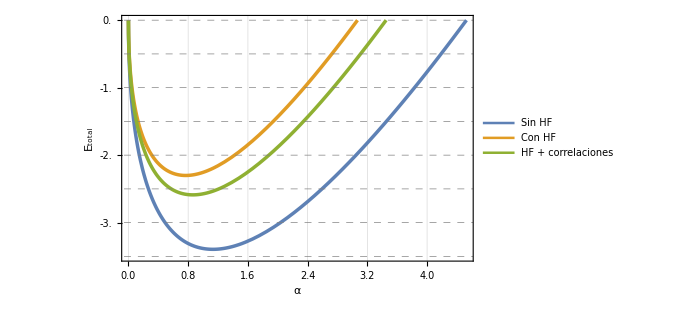

```mathematica
x0=0;xf=4.527;
fig=Plot[{En[α],EHF[α],EDFT[α]},{α,x0,xf},PlotStyle->Directive[Thickness[0.005]],Frame->True,ImageSize->500,PlotRange->{{x0,xf},{-3.5,0}},PlotLegends->{"Sin HF", "Con HF", "HF + correlaciones"},LabelStyle->Directive[Black,FontSize->15,FontFamily->"Sans Serif"],FrameLabel->{"α","E_total"},FrameTicks->{{Table[-i,{i,0,3.5,0.5}],Table[-i,{i,0,3.5,0.5}]},{Automatic,None}},GridLines->{Automatic,Table[-i,{i,0,3.5,0.5}]},GridLinesStyle->Directive[Thin,Gray,Dashed]]
```

```mathematica
Export["/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/fig_tarea06.pdf",fig]
```

/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/fig_tarea06.pdf